Let's define the wavefunctions:

```mathematica
φ[n_,x_]:=√(2/L)Sin[(n*π*x)/L]
ψ[x_]:=1/(√2)φ[1,x]+1/(√2)φ[2,x]
```

The probability density is then

```mathematica
P[x_,t_]:=1/2 φ[1,x]^2+1/2 φ[2,x]^2+φ[1,x]*φ[2,x]*Cos[t/h(Subscript[E, 2]-Subscript[E, 1])]
```

```mathematica
L=4;
```

Here is a plot of probability density at times t = 0, τ/8, τ/4,(3τ)/8 τ/2,(3τ)/4,τ.

```mathematica
τ=(2*π*h)/(Subscript[E, 2]-Subscript[E, 1]);
```

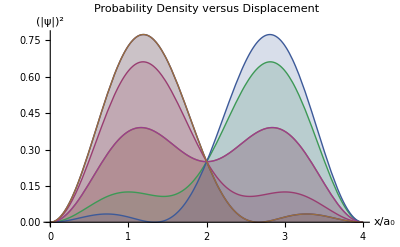

```mathematica
Plot[{P[x,0],P[x,τ/8],P[x,τ/4],P[x,(3τ)/8],P[x,τ/2],P[x,(3τ)/4],P[x,τ]},{x,0,4},PlotLabel->"Probability Density versus Displacement",Filling->Axis,AxesLabel->{x /Subscript[a, 0],(|ψ|)^2}]
```

Here is animated plot of the time evolution of the probability density

```mathematica
Animate[Plot[P[x,t*τ],{x,0,4},PlotRange->{-.5,1.2},Filling->Axis,AxesLabel->{x /Subscript[a, 0],(|ψ|)^2}],{t,0,1}]
```

As we can see from the time evolution of the probability density the area under the curve is always unity.